# Image Parametric Equation Generator

## Configuration Section

```mathematica
imgURL = "http://cartoonbros.com/wp-content/uploads/2016/08/pikachu-3.png"; (* Image URL *)
```

## Code Section

```mathematica
(image =Import[imgURL])//Show[#, ImageSize -> 360]&
```

-Graphics-

```mathematica
(edgeImage=Thinning[EdgeDetect[ColorConvert[
ImagePad[Image[Map[Most, ImageData[image],{2}]],20, White], "Grayscale"]]])//
Show[#, ImageSize -> 360]&
```

-Graphics-

```mathematica
edgePoints = {#2, -#1}&@@@ Position[ImageData[edgeImage],1,{2}];
```

```mathematica
pointListToLines[pointList_, neighborhoodSize_:6]:= 
Module[{L = DeleteDuplicates[pointList], NF, λ,lineBag, counter, seenQ, sLB, nearest,  
            nearest1, nextPoint,couldReverseQ,  𝒹, 𝓃, 𝓈},
NF = Nearest[L] ;
     λ = Length[L];
Monitor[
(* list of segments *)
lineBag = {};
counter = 0; 
While[counter < λ,
(* new segment *)
sLB = {RandomChoice[DeleteCases[L, _?seenQ]]}; 
seenQ[sLB[[1]]]=True;
counter++;
couldReverseQ= True;
(* complete segment *)
While[(nearest = NF[Last[sLB], {Infinity, neighborhoodSize}];
           nearest1 = SortBy[DeleteCases[nearest, _?seenQ], 1.EuclideanDistance[Last[sLB],#]&];
           nearest1 =!= {} || couldReverseQ),
             If[nearest1 === {},
             (* extend the other end; penalize sharp edges *)
             sLB = Reverse[sLB]; couldReverseQ = False,
            (* prefer straight continuation *)
             nextPoint = If[Length[sLB] ≤ 3, nearest1[[1]],
                                         𝒹 = 1.Normalize[(sLB[[-1]]-sLB[[-2]]) + 1/2 (sLB[[-2]]-sLB[[-3]])];
                                         𝓃 = {-1, 1}Reverse[𝒹];
                                        𝓈 = Sort[{Sqrt[(𝒹.(# - sLB[[-1]]))^2 + 
                                                           (* perpendicular *) 2 (𝓃.(# - sLB[[-1]]))^2], # }& /@ nearest1]; 
                                        𝓈[[1,2]]];
             AppendTo[sLB, nextPoint];
            seenQ[nextPoint]=True;
           counter++ ]];
AppendTo[lineBag, sLB]];
(* return segments sorted by length *)
Reverse[SortBy[Select[lineBag , Length[#] > 12&], Length]],
(* monitor progress *)
Grid[{{Text[Style["progress point joining", Darker[Green, 0.66]]], ProgressIndicator[counter/λ]},
          {Text[Style["number of segments", Darker[Green, 0.66]]],  Length[lineBag] + 1}}, 
        Alignment -> Left, Dividers -> Center]]]
```

```mathematica
SeedRandom[22];
hLines = pointListToLines[edgePoints, 6];
Length[hLines]
```

15

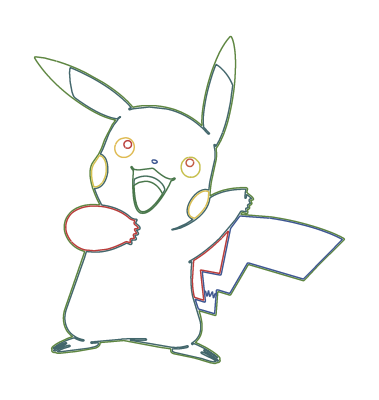

```mathematica
Graphics[{ColorData["DarkRainbow"][RandomReal[]], Line[#]}& /@ hLines]
```

```mathematica
Graphics[BSplineCurve[#, SplineDegree -> 6, SplineClosed -> True]& /@ hLines]
```

-Graphics-

```mathematica
(* Fourier coefficients of a single curve *)
fourierComponentData[pointList_, nMax_, op_] := 
Module[{ε=10^-3, μ = 2^14, M = 10000,s,
             scale, Δ, L , nds, sMax, if, 𝓍𝓎Function, X, Y, XFT, YFT,type},
(* prepare curve *)
scale = 1. Mean[Table[ Max[ fl/@ pointList] - Min[fl /@ pointList],{fl,{First, Last}}]];
 Δ=EuclideanDistance[First[pointList], Last[pointList]];
 L=Which[op === "Closed", type="Closed";
                                                        If[First[pointList]===Last[pointList], 
                                                           pointList,Append[pointList, First[pointList]]], 
                op === "Open",type="Open";pointList,
                 Δ==0.,type="Closed";  pointList,
                 Δ/scale<op, type="Closed"; Append[pointList, First[pointList]],
                True,  type="Open"; Join[pointList, Rest[Reverse[pointList]]]];
(* re-parametrize curve by arclength *)
𝓍𝓎Function =BSplineFunction[L, SplineDegree->4];
nds = NDSolve[{s'[t]==Sqrt[𝓍𝓎Function'[t].𝓍𝓎Function'[t]], s[0]==0},s, 
                          {t, 0, 1}, MaxSteps -> 10^5, PrecisionGoal -> 4];
(* total curve length *)
     sMax= s[1]/.nds[[1]];
     if=Interpolation[Table[{s[σ]/.nds[[1]], σ}, {σ,0, 1, 1/M}]];
X[t_Real] :=  BSplineFunction[L][Max[Min[1, if[(t +Pi)/(2Pi)sMax]] , 0]][[1]];
Y[t_Real] :=  BSplineFunction[L][Max[Min[1, if[(t +Pi)/(2Pi)sMax]] , 0]][[2]]; 
(* extract Fourier coefficients *)
{XFT, YFT} = Fourier[Table[#[N @ t], {t, -Pi+ε, Pi - ε, (2Pi-2ε)/μ}]]& /@ {X, Y};   
{type,2Pi/Sqrt[μ] *
((Transpose[Table[{Re[#], Im[#]}&[Exp[I k Pi]  #[[k+1]]], {k, 0, nMax}]]& /@ {XFT, YFT}))}  ]
```

```mathematica
Options[fourierComponents] = {"MaxOrder" -> 180, "OpenClose" -> 0.025};

fourierComponents[pointLists_,OptionsPattern[]] := 
Monitor[Table[fourierComponentData[pointLists[[k]],                           
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["MaxOrder"]],
                                                                      If[Head[#]===List, #[[k]], #]&[ OptionValue["OpenClose"]]],
                         {k, Length[pointLists]}],
Grid[{{Text[Style["progress calculating Fourier coefficients", Darker[Green, 0.66]]], ProgressIndicator[k/Length[pointLists]]} }, 
        Alignment -> Left, Dividers -> Center]]/; Depth[pointLists] === 4
```

```mathematica
fCs = fourierComponents[hLines];
```

```mathematica
sinAmplitudeForm[kt_, {cF_, sF_}] := With[{φ = phase[cF, sF]}, Sqrt[cF^2+sF^2] Sin[kt+ φ]]

phase[cF_, sF_] := With[{T = Sqrt[cF^2+sF^2]},
With[{g = Total[Abs[Table[cF Cos[x] +sF Sin[x]-  T Sin[x+#1 ArcSin[cF/T]+#2],{x, 0, 1, 0.1}]]]&}, 
          If[g[1, 0]<   g[-1, Pi],  ArcSin[cF/T],Pi-ArcSin[cF/T]]]]
```

```mathematica
singleParametrization[fCs_, t_, n_] :=
 UnitStep[Sign[ Sqrt[Sin[t/2]]]] *
 Sum[UnitStep[t-((m -1)4Pi-Pi)]UnitStep[(m -1)4Pi + 3 Pi-t]*
({+fCs[[m,2, 1, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 1, 1, k+1]], fCs[[m,2, 1, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}],   
 +fCs[[m,2, 2, 1, 1]]/2+Sum[sinAmplitudeForm[k t, {fCs[[m,2, 2, 1, k+1]], fCs[[m,2, 2, 2, k+1]]}], 
{k,Min[If[Head[n]===List, n[[m]],n], Length[fCs[[1 ,2, 1, 1]]]]}]} ),
{m, Length[fCs]}]
```

```mathematica
makeFourierSeries[{"Closed" | "Open", {{cax_, sax_},{cay_, say_}}}, t_, n_] :=
 {Sum[If[k==0, 1/2, 1]cax[[k+1]] Cos[k t]+sax[[k+1]] Sin[k t],{k,0, Min[n, Length[cax]]}],
 Sum[If[k==0, 1/2, 1]cay[[k+1]] Cos[k t]+say[[k+1]] Sin[k t],{k, 0,Min[n, Length[cay]]}]}
```

```mathematica
makeFourierSeriesApproximationManipulate[fCs_, maxOrder_:60] :=
Manipulate[
With[{opts = Sequence[PlotStyle -> Black, Frame -> True, Axes -> False, 
                                         FrameTicks -> None,PlotRange -> All, ImagePadding -> 12]},
Show[{
ParametricPlot[Evaluate[ makeFourierSeries[#,t, n]& /@ Cases[fCs, {"Closed", _}]], {t, -Pi, Pi},opts],
ParametricPlot[Evaluate[ makeFourierSeries[#,t, n]& /@ Cases[fCs, {"Open", _}]], {t, -Pi, 0},opts]}] // Quiet], 
{{n, 1, "max series order"}, 1, maxOrder,1,Appearance -> "Labeled"},
TrackedSymbols :> True, SaveDefinitions -> True]
```

## Output Section

```mathematica
(* You can change the number of terms in the Fourier decomposition to see how it affects the image. *)
makeFourierSeriesApproximationManipulate[fCs, 180]
```

```mathematica
<<ToMatlab` (* Load ToMatlab *)
```

```mathematica
nTerm = 100; (* Number of terms in your Fourier decompositon, maximum is 180. *)
finalCurve = Rationalize[singleParametrization[fCs, t,nTerm] ,10^-3];
StringReplace[StringReplace[ToMatlab[finalCurve],"UnitStep"->"heaviside"], "Sign"->"sign"]
```